# Specification

## Diary stores

Represents all data about the diaries. Stores data about observations as well as information about how complete the data is.

```mathematica
<|
"Observations"->{_DiaryObservation...},
"Progress"-><|
(*OraccID*)->(*status*),
"X301581"->"Incomplete"|"Complete"|"Reviewed",
...
|>
|>
```

## DiaryObservation

Represents an observation.

```mathematica
DiaryObservation[<|
"Type"->_String(*The type of observation (RelativePosition, WindDirection, etc)*),
"Content"-><|...|>(*The content of the observation*),
"Inferred"->{...}(*The list of keys in Content which were inferred*),
"Date"->DiaryCombinedDate[...],
"UUID"->_String(*UUID for identifying this observation*),
"Provenance"-><|
"Creator"->_String(*Creator name*),
"TabletID"->_String(*Oracc ID (for example, X301440)*),
"LineNumber"->_Integer(*The line number in the reference copoy of Oracc*),
"Reviewed"->True|False(*Whether this observation reviewed*),
"Notes"->_String|_Missing(*Any notes about the provenance*)
|>
|>]
```

## Observation types

### General astronomical

#### RelativePosition

Represents the relative position of two objects, as usually written in the main body of each month.

```mathematica
<|
"Object"->_Entity|_Missing(*Primary object*),
"Reference"->_Entity|_Missing(*Secondary object*),
"Displacements"->{
{_DiaryDistance|_Missing,"InFrontOf"|"Behind"|"East"|"West"|"Above"|"Below"|"North"|"South"|_Missing}(*First displacement mentioned*),
{_DiaryDistance|_Missing,"InFrontOf"|"Behind"|"East"|"West"|"Above"|"Below"|"North"|"South"|_Missing}(*Second displacement mentioned*)}
|>
```

#### ZodiacalPosition

Represents an observation that an object was in a sign of the zodiac. This should be used for end of month summaries as well as for things like first appearances.

```mathematica
<|
"Object"->_Entity|_Missing,
"Sign"->_Entity|_Missing,
"Entering"->True|False(*whether this is the first day when this object entered ("reached") this sign*),
"PositionInSign"->"Beginning"|"End"|_Missing
|>
```

#### NamedPosition

Represents an observation that an object was in some named region in the sky. For example, “Mars became stationary in the area of the Lip of the Scorpion”.

```mathematica
<|
"Object"->_Entity|_Missing,
"Name"->_String
|>
```

#### Visible

Represents a note that an object was visible. This is common in eclipse reports.

```mathematica
<|
"Object"->_Entity|_Missing
|>
```

#### NotVisible

Represents a note that an object was not visible. This is common in end of month summaries when the sign of the zodiac would otherwise be recorded, as well as in eclipse observations.

```mathematica
<|
"Object"->_Entity|_Missing
|>
```

#### Solstice

Represents a solstice. These were likely predicted for most of the diaries.

```mathematica
<|
"IdealDate"->_DiaryBabylonianDate|_Missing,
"DidNotWatch"->True|False
|>
```

#### Equinox

Represents an equinox. These were likely predicted for most of the diaries.

```mathematica
<|
"IdealDate"->_DiaryBabylonianDate|_Missing,
"DidNotWatch"->True|False
|>
```

#### Eclipse

Represents an observation of an eclipse.

```mathematica
<|
"EclipseType"->"Lunar"|"Solar",
"Observed"->True|False(*Whether the eclipse was observed or predicted*),
"MoonriseToSunset"->_String|_Missing(*Subobservation*),
"SunriseToMoonset"->_String|_Missing(*Subobservation*),
"StartTime"->_DiaryCulminatingTime|_Missing,
"EntranceDirection"->"North"|"South"|"East"|"West"|"Northeast"|"Northwest"|...|_Missing,
"StartToMaxPhase"->_DiaryDuration|_Missing,
"MaxPhase"->{_DiaryDistance|_Missing,"Magnitude"|"Remaining"(*Whether the magnitude was 4 fingers, or there were 4 fingers remaining to totality*)}|"Total"|_Missing,
"MaxPhaseDuration"->_DiaryDuration|_Missing,
"MaxPhaseToEnd"->_DiaryDuration|_Missing(*Time between end of max phase and eclipse*),
"MovementDirection"->"North"|"South"|"East"|"West"|"Northeast"|"Northwest"|...|_Missing,
"TotalDuration"->_DiaryDuration|_Missing,
"Weather"->{_String...}(*Weather related subobservations*),
"ObjectVisibilities"->{_String...}(*Visible and NotVisible subobservations*),
"LunarPosition"->_String|_Missing(*Subobservation of the relative position of the Moon*),
"SunsetToStart"->_DiaryDuration|_Missing,
"StartToSunrise"->_DiaryDuration|_Missing
|>
```

### Planetary (“Greek-Letter”) phenomena

#### FirstAppearenceEast (Γ)

Records the first appearance of an inner planet in the east. Also used for the first visibility of outer planets.

```mathematica
<|
"Object"->_Entity|_Missing,
"VisibilityDuration"->_DiaryDuration|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryBabylonianDate|_Missing,
"Position"->_String|_Missing(*Subobservation of position*)
|>
```

#### FirstAppearenceWest (Ξ)

Records the first appearance of an inner planet in the west.

```mathematica
<|
"Object"->_Entity|_Missing,
"VisibilityDuration"->_DiaryDuration|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryBabylonianDate|_Missing,
"Position"->_String|_Missing(*Subobservation of position*)
|>
```

#### LastAppearenceEast (Σ)

Records the last appearance of an inner planet in the east.

```mathematica
<|
"Object"->_Entity|_Missing,
"VisibilityDuration"->_DiaryDuration|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryBabylonianDate|_Missing,
"Position"->_String|_Missing(*Subobservation of position*)
|>
```

#### LastAppearenceWest (Ω)

Records the last appearance of an inner planet in the west. Also used for last visibility for outer planets.

```mathematica
<|
"Object"->_Entity|_Missing,
"VisibilityDuration"->_DiaryDuration|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryBabylonianDate|_Missing,
"Position"->_String|_Missing(*Subobservation of position*)
|>
```

#### FirstStationaryPoint (Φ)

Records the first station of an inner planet or outer planet. This is often called the stationary point “in the east” for inner planets.

```mathematica
<|
"Object"->_Entity|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryBabylonianDate|_Missing,
"Position"->_String|_Missing(*Subobservation of position*)
|>
```

#### SecondStationaryPoint (Ψ)

Records the second station of an inner planet or outer planet. This is often called the stationary point “in the west” for inner planets.

```mathematica
<|
"Object"->_Entity|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryBabylonianDate|_Missing,
"Position"->_String|_Missing(*Subobservation of position*)
|>
```

#### AcronychlRising (Θ)

Records the acronychal rising of an outer planet. This is often referred to as “opposition” in translations.

```mathematica
<|
"Object"->_Entity|_Missing,
"DidNotWatch"->True|False,
"IdealDate"->_DiaryBabylonianDate|_Missing
|>
```

### Lunar Six

#### SunsetToMoonset

The duration between sunset to moonset recorded at the beginning of the month.

```mathematica
<|
"Duration"->DiaryDuration[...]|_Missing,
"DidNotWatch"->True|False,
"Measured"->True|False
|>
```

#### MoonsetToSunrise

The duration between moonset and sunrise.

```mathematica
<|
"Duration"->DiaryDuration[...]|_Missing,
"DidNotWatch"->True|False,
"Measured"->True|False
|>
```

#### SunriseToMoonset

The duration between sunrise and moonset.

```mathematica
<|
"Duration"->DiaryDuration[...]|_Missing,
"DidNotWatch"->True|False,
"Measured"->True|False
|>
```

#### MoonriseToSunset

The duration between moonrise and sunset.

```mathematica
<|
"Duration"->DiaryDuration[...]|_Missing,
"DidNotWatch"->True|False,
"Measured"->True|False
|>
```

#### SunsetToMoonrise

The duration between sunset and moonrise.

```mathematica
<|
"Duration"->DiaryDuration[...]|_Missing,
"DidNotWatch"->True|False,
"Measured"->True|False
|>
```

#### MoonriseToSunrise

The duration between moonrise and sunrise recorded at the end of the month.

```mathematica
<|
"Duration"->DiaryDuration[...]|_Missing,
"DidNotWatch"->True|False,
"Measured"->True|False
|>
```

### Weather

#### WindDirection

Represents an observation that “the __ wind blew”. See the Weather observation type for things like “gusty wind blew”.

```mathematica
<|
"Direction"->"North"|"South"|"East"|"West"|_Missing
|>
```

#### Weather

Represents generalized weather.

Note: better tags could likely be made with heavier reference to the original Akkadian terms.

```mathematica
<|
"Tag"->"Mist"|"Rain"|"Clouds"|"ThinClouds"|"CrossingClouds"|"HeavyClouds"|"Fog"|"HeavyFog"|"Lightning"|"Thunder"|"Haze"|"Mud"|"ThickRain"|"Hail"|"Dew"|"Cloudburst"|"Cold"|"ColdWind"|"Overcast"|"Locusts"|{"Rainbow","North"|"South"|"East"|"West"|_Missing}|{"Halo","North"|"South"|"East"|"West"|_Missing}
|>
```

### Miscellaneous

#### MarketRates

Represents the prices of various commodities mentioned in the end of month summaries. The quantity of each commodity is the amount that can be bought for 1 shekel of silver. This is essentially the reciprocal of the price.

Note: these keys rely on the translations from Sachs and Hunger. They note that the translations for “Cress” and “Mustard” are uncertain.

```mathematica
<|
"Barley"->_DiaryCapacity|_Missing,
"Dates"->_DiaryCapacity|_Missing,
"Mustard"->_DiaryCapacity|_Missing,
"Cress"->_DiaryCapacity|_Missing,
"Sesame"->_DiaryCapacity|_Missing,
"Wool"->_Integer|_Rational|_Missing(*Weight in minas (approximately pounds)*)
|>
```

The following is used to mark when sales were “cut off”:

```mathematica
Missing["SalesCutOff"]
```

#### RiverLevelDirection

Represents an observation that the river level was rising, falling, or standing still on a particular day.

```mathematica
<|
"Direction"->"Rising"|"Falling"|"Standing"|_Missing,
|>
```

#### RiverLevelChange

Represents an observation that the river level changed from one day to another. Reported on the end date of the interval.

```mathematica
<|
"StartDate"->_DiaryCombinedDate|_Missing,
"Direction"->"Rising"|"Falling"|"Standing"|_Missing,
"Distance"->_DiaryDistance|_Missing,
"Remainder"->_DiaryDistance|_Missing
|>
```

#### RiverLevel

Represents an observation of the absolute river level on the na-gauge. Each unit on the na is equivalent to 4 fingers or 1/6 cubits.

```mathematica
<|
"Value"->_Integer|_Rational|_Missing(*Value on the na-gauge*)
|>
```

#### HistoricalEvent

Represents a historical event, often mentioned at the end of the month.

```mathematica
<|
"EndLine"->_Integer,(*the last line containing this event (for text extraction)*)
"Tags"->{"War"|"ReligiousCeremony"|"Famine"|"Celebration"..}(*INCOMPLETE*)
|>
```

#### Error

Represents an error in the original diaries. For example, when the wrong day is written, or when they write “west” instead “south”, etc. These are often errors which make it so that it is impossible to encode observations because they do not follow the standard structure.

```mathematica
<|
"Type"->String(*Type of observation being attempted*),
"Note"->String
|>
```

#### Other

Represents a observation that does not fit in the current version of the format. These can be tagged so if the format is updated to support these observations, it will be possible to go back and find them.

```mathematica
<|
"Tags"->{_String..},
"Note"->String|_Missing
|>
```

## Helper types

#### DiaryDate

Represents a date in a combination of the Julian and Babylonian calendars. Dates are aligned based on their daylight hours.

```mathematica
DiaryJulianDate[{
_Integer|_Missing(*Year AD*),
_Integer|_Missing(*Month*),
_Integer|_Missing(*Day*)
}]
```

```mathematica
DiaryBabylonianDate[{
{_String(*King*),_Integer(*Year*)}|_Missing,
_String|_Missing(*Month*),
_Integer|"Middle"|"End"|_Missing(*Day*)
}]
```

```mathematica
DiaryCombinedDate[<|
"JulianDate"->_DiaryJulianDate|_Missing,
"BabylonianDate"->_DiaryBabylonianDate|_Missing,
"Time"->"BeginningOfTheNight"|"FirstPartOfTheNight"|"MiddlePartOfTheNight"|"LastPartOfTheNight"|"Morning"|"Noon"|"Afternoon"|"Sunset"|"Day"|"Night"|_Missing
|>]
```

```mathematica
$DiaryChronology
```

“Day” and “Night” can be used in to distinguish observations like “The night of the 19th, ...” or “The 19th, ...”

Below is the list of king names for regnal years:

```mathematica
{"Šamaššumukin","NebukadnezarII","ArtaxerxesI","DariusII","ArtaxerxesII","ArtaxerxesIII","DariusIII","AlexanderIII","PhilipArrhidaeus","AlexanderIV","SE"}
```

#### DiaryDistance

Represents a distance in cubits (KÙŠ) and fingers (ŠI or U).

```mathematica
DiaryDistance[{_Integer|_Rational|_Missing(*cubits*),_Integer|_Missing(*fingers*)}]
```

Can also represent non-numerical distances.

```mathematica
DiaryDistance["ALittle"|...]
```

Note: more non-numerical distances should be added.

#### DiaryDuration

Represents a duration. Often used for Lunar Six quantities.

```mathematica
DiaryDuration[{(*bēr*),(*Degrees/UŠ*),(*ArcMinutes/NINDA*)}]
```

#### DiaryCulminatingTime

Represents a time by a culminating (ziqpu) star and an adjustment.

```mathematica
DiaryCulminatingTime[<|
"CulminatingStar"->_Entity|_Missing,
"Adjustment"->_DiaryDuration|_Missing,
"AdjustmentDirection"->"InFrontOf"|"Behind"|_Missing
|>]
```

#### DiaryCapacity

Represents an amount of barely, dates, mustard, cress, or sesame in MarketRates observations.

```mathematica
DiaryCapacity[{(*kur*),(*pān*),(*sūt*),(*qa*)}]
```

Each commodity is 0 if unmentioned in the diary (instead of Missing[“Unmentioned”]) and only _Missing if explicitly destroyed.

## Generalized missing types

Represents data that is missing for an unspecified or unknown reason. Use Missing[“Unmentioned”] if it is clearly not mentioned, and Missing[] only for cases where it is not clear what kind of Missing[...] to use.

```mathematica
Missing[]
```

Represents data that was clearly destroyed on the original tablet. For example “the moon was [...] cubits ahead of β Capricorni”:

```mathematica
Missing["Destroyed"]
```

Represents data that was explicitly not mentioned. For example, “the moon was ahead of β Capricorni” (where the distance is unmentioned):

```mathematica
Missing["Unmentioned"]
```

There are other missing types that are specific to observation types (for example, Missing[“SalesCutOff”] in MarketRates observations.)

## Input format

There is a simplified inputting format designed for inputting data. Running processInputFormat on this converts it into the full format specified above. The following shows the basic form of the input format:

```mathematica
{
<|
"TabletID"->_String,
"Creator"->_String,
"Months"->{
<|
"BabylonianYear"->{_String|_Missing,_Integer|_Missing}|_Missing,
"BabylonianMonth"->_String|_Missing,
"Observations"->{
DiaryObservation[...],
<|
"UUID"->_String,
"LineNumber"->_Integer,
"Date"->DiaryInputDate[(*day of the month*),(*time*)]|DiaryInputDate[(*day of the month*)]|_DiaryCombinedDate|_Missing,
"Type"->_String,
"Inferred"->{...},
"Content"-><|...|>,
"Notes"->_String|_Missing
|>,
...
}
|>
}
|>
}
```

Dates that appear inside of observations (like with “IdealDate”) can use inputMonthDay[n, time] to represent a day and time in the specified month.

# Examples

Load the paclet:

```mathematica
Quit
```

```mathematica
PacletDirectoryLoad["~/git/errorhandling/"];
PacletDirectoryLoad[FileNameJoin[{ParentDirectory@NotebookDirectory[],"packages"}]];
```

```mathematica
Get["ComputationalDiaries`"]
```

```mathematica
?ComputationalDiaries`*
```

```mathematica
DiaryCurationPalette[]
```

p9689_shm157FrontEndObject[LinkObject["p9689_shm", 3, 1]]157Curation

```mathematica
DiaryJulianDate[{-127,3,6}]["DateObject"]
```

Day: Mon 6 Mar -128 (Juliancalendar)

```mathematica
DiaryJulianDate[{-1,3,6}]["DateObject"]
```

Day: Thu 6 Mar -2 (Juliancalendar)

```mathematica
DiaryAstronomicalPosition[Entity["PlanetaryMoon","Moon"],Now]
```

{34.7899,-3.88396}

```mathematica
DiaryTabletText[]
```

```mathematica
DiaryTabletTable["X102611"]
```

(o 1') | 1 | Month II, (the 1st of which was identical with) the 30th (of the preceding month), [sunset to moonset:] 12° [...]
(o 2') | 2 | Night of the 8th, first part of the night, Mercury was [... above η Geminorum ...]
(o 3') | 3 | Night of the 11th, beginning of the night, the moon was [...] in front of [α Virginis ...]
(o 4') | 4 | The 14th, moonset to sunrise: 8° 50'. Night of the 1[5th, ...]
(o 5') | 5 | The 16th, Sirius’ last appearance. Night of the 17th, ... [...]
(o 6') | 6 | 1 2/3 cubits [...] Capricorni [...]
(o 7') | 7 | That [month,] the equivalent (for 1 shekel of silver was): ba[rley, ...]
(o 8') | 8 | [...] ... [...]
(r 1') | 9 | [...] ... on the ... [... Mars was ...]
(r 2') | 10 | in the middle of the month, in Cancer. Th[at month, ...]
(r 3') | 11 | That month, Paini ... [...]
 |  | 
(r 4') | 12 | Month VI, (the 1st of which was identical with) the 30th (of the preceding month, sunset to moonset:) 9° 30'; mist, when I watched [I did not see the moon ... Night of the 5th, beginning of the night, the moon was]
(r 5') | 13 | 1 cubit 4 fingers behind α Scorpii. Night of the 6th, [...]
(r 6') | 14 | Night of the 9th, beginning of the night,  the moon was [... behind β Capricorni ...]
(r 7') | 15 | The 12th, moonset to sunrise: 11°. The 13th, 2° [... Night of the 15th, last part of the night, the moon was]
(r 8') | 16 | [...] below α Arietis [...]
(r 9') | 17 | last part of the night,, the moon was [...] in front of [...]
(l.e. 1) | 18 | [... year 5]0, Antiochus, the great king [...]

```mathematica
DiaryCurationPalette[]
```

```mathematica
dataDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"curatedData"}]
```

/Users/christopher/git/ComputationalDiaries/curatedData

```mathematica
$DiaryChronology=Join@@Import/@FileNames["chronology.mx",Select[FileNames["*",dataDirectory],DirectoryQ]];
```

```mathematica
observations=Join@@Import/@FileNames["observations.mx",Select[FileNames["*",dataDirectory],DirectoryQ]];
```

```mathematica
Length[observations]
```

112

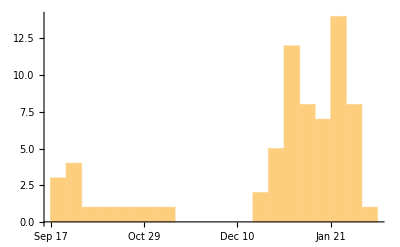

```mathematica
DateHistogram[Enclose[Confirm[#["Date"]["JulianDate"]]["DateObject"],"Expression"]&/@observations,"Week"]
```

```mathematica
ReverseSort@Counts[#["Type"]&/@observations]
```

<|Weather→39,RelativePosition→28,ZodiacalPosition→8,MarketRates→5,NotVisible→4,HistoricalEvent→3,Other→3,Visible→3,FirstAppearenceEast→2,MoonriseToSunrise→2,SunsetToMoonrise→2,MoonsetToSunrise→2,FirstStationaryPoint→1,NamedPosition→1,Equinox→1,SunriseToMoonset→1,MoonriseToSunset→1,SunsetToMoonset→1,RiverLevel→1,RiverLevelChange→1,LastAppearenceWest→1,AcronychalRising→1,LastAppearenceEast→1|>

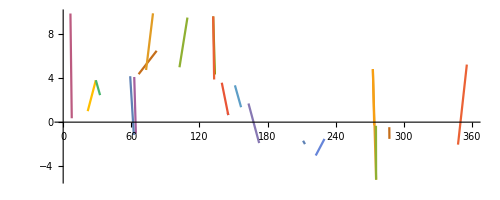

```mathematica
ListLinePlot[DeleteMissing[Enclose[{Confirm@DiaryAstronomicalPosition[Confirm[#["Object"]],Confirm[#["Date"]]],Confirm@DiaryAstronomicalPosition[Confirm[#["Reference"]],Confirm[#["Date"]]]},"Expression"]&/@Select[observations,#["Type"]==="RelativePosition"&]],PlotRange->{{0,360},All},AspectRatio->Automatic]
```

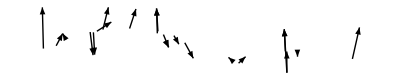

```mathematica
Graphics[{Arrowheads[Small],Arrow[DeleteMissing[Enclose[{Confirm@DiaryAstronomicalPosition[Confirm[#["Object"]],Confirm[#["Date"]]],Confirm@DiaryAstronomicalPosition[Confirm[#["Reference"]],Confirm[#["Date"]]]},"Expression"]&/@Select[observations,#["Type"]==="RelativePosition"&]]]},PlotRange->{{0,360},All}]
```

## Ideas

Add more error checking to DiaryObservation

More algebra of missing

Use Time more in DiaryDate

Implement DiaryCulminatingTime

Add bēr to implementation of DiaryDuration

Make astronomicalPosition support arbitrary stars

Update curation palette for new types

Add “balanced” for RelativePositions?

Should DiaryDisplacement be merged with the RelativePosition observation type, and its methods made DiaryObservation methods?

Add and document many DiaryObservation methods

Add eclipses to the curation palette

Check the time parameters of the dates on the curation palette. Most are unnecessary.

EntityStore interface?

Should DiaryDistance be signed?

Deal with these observations:

Consider meteor and comet observation types

How to mark when observations apply to the end of the month? This is particularly important for the end-of-month report on the visibilities of planets.

Text analysis: look at the distribution of the “night of the __th”. Did they have nights off?

Should Missing[“Unmentioned”] replace False in properties like DidNotWatch or Measured?

#### Meteor [INCOMPLETE]

Represents an observation of a meteor.

Note: should Tags be included? How to encode direction?

```mathematica
<|
"Tags"->{"Torch"|"Bright"...},
"Direction"->
|>
```

#### Comet [INCOMPLETE]

Represents an observation of a comet.

Note: should Tags be included? If so, finish the list of tags.

```mathematica
<|
"Tags"->{"Torch"|"Bright"...}
|>
```